```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

Remove::rmnsm: There are no symbols matching ""Global`*"". ButtonBox["»", Appearance->{Automatic, None}, BaseStyle->"Link", ButtonData:>"paclet:ref/message/Remove/rmnsm", ButtonNote->"Remove::rmnsm"]

```mathematica
SetDirectory["~/Work/data/01mar17"]
```

/home/andrew/Work/data/01mar17

```mathematica
dat=Import["AllSpins.txt","Table"];
(*originGS=Import["gsorigin.dat","Table"];*)
actualGS=Import["ground_states.dat","Table"];
```

```mathematica
mag1=Import["n1.000_.00001/fort.1","Table"]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
mag=mag1[[All,2]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
Length[dat]
```

68

```mathematica
nspins=(Length[dat])/4
spins=Table[{0,0,0},{i,1,nspins}];
```

17

```mathematica
Length[spins]
```

17

```mathematica
Do[spins[[i,1]]=dat[[4i-2]];
spins[[i,2]]=dat[[4i-1]];
spins[[i,3]]=dat[[4i]],{i,1,nspins}]
```

Check (the last) spin configuration against the file.

```mathematica
spins[[1]]//MatrixForm
```

(0.7361203422106805696 | 0.5892090828304813546 | -0.3331058367751809483
0.6650752044564690773 | -0.458811103971175502 | 0.5892090828304813546
0.6650752044564690773 | -0.458811103971175502 | 0.5892090828304813546)

Check the Byron relationship

```mathematica
tol=10^-6;
Do[Print["config",i-1," check a ",If[spins[[i,1,1]]+spins[[i,2,3]]<tol,0,"oops"], 
" check e ",
If[ spins[[i,2,2]]+spins[[i,3,1]]<tol,0,"oops"],
" check d ",
If[spins[[i,2,1]]+spins[[i,1,3]]+spins[[i,3,2]]<(tol),0,"oops"]],{i,1,1}]
```

config0 check a oops check e oops check d 0

Now let’s take a look at what θ and ϕ values Andrew’s configurations correspond to.

tan ϕ = b/a (= sinθ sinϕ / sinθ cosϕ = y/x)
ArcTan[x,y]
cosθ=c

```mathematica
theta=Table[0,{i,1,nspins}];
phi=Table[0,{i,1,nspins}];
Do[theta[[i]]=ArcCos[spins[[i,1,3]]];
phi[[i]]=ArcTan[spins[[i,1,1]],spins[[i,1,2]]],{i,1,nspins}]
```

```mathematica
Bound[ϕ_]:=If[Cos[4 ϕ]==1,π/3,ArcSin[√((4-√(16-6(1-Cos[4 ϕ])))/(1-Cos[4ϕ]))]]
```

```mathematica
??Diamond
```

RowBox[{"Diamond", "[", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "]"}] displays as RowBox[{StyleBox["x", "TI"], "⋄", StyleBox["y", "TI"], "⋄", StyleBox["…", "TR"]}].

```mathematica
marker1=Graphics[{RGBColor[0.22,0.6,0.32],Disk[]}];
marker2=Graphics[{RGBColor[0.13,0.83,1],Disk[]}];
```

ListPlot::lpn: originGS is not a list of numbers or pairs of numbers.

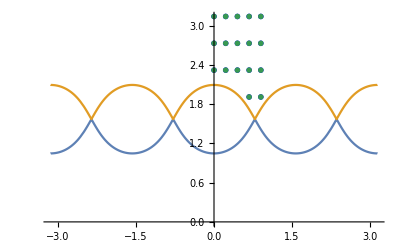

```mathematica
gsPlot=ListPlot[originGS,PlotStyle->Orange];
confPlot=ListPlot[Transpose[{phi,theta}],Frame->{True,True,False,False},FrameLabel->{"ϕ","θ"},Axes->False,PlotRangePadding->Automatic,PlotMarkers->{marker1,0.03}];
actGSPlot=ListPlot[actualGS,PlotStyle->Blue,PlotMarkers->{"X",20}];
boundPlot=Plot[{Bound[ϕ],π-Bound[ϕ]},{ϕ,-π,π},PlotRange->{{-180Degree,180Degree},{0,π}}];
Show[boundPlot,actGSPlot,confPlot]
```

```mathematica
ArcCos[1]
```

0

```mathematica
1/9
```

1/9

```mathematica
1/(√3)//N
```

0.57735

```mathematica
θ=ArcCos[0.5773502691896258]
```

```mathematica
0.9553166181245092
```

0.955317

```mathematica
ϕ=ArcCos[1/(√3*Sin[θ])]
```

```mathematica
0.7853981633974483
```

0.785398

```mathematica
Vector={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}
```

{0.57735,0.57735,0.57735}

```mathematica
Norm[Vector]
```

1.